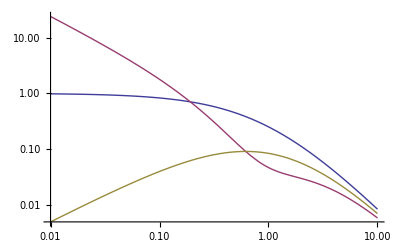

{{x→0.191488}}

{{x→0.618034}}

```mathematica
f0[x_]:=1/(1+x)^2
f1[x_]:=2/(1+x)^2
f2[x_]:=2(1+x)^2/x/(2+x)^3
f3[x_]:=2/(1+x)/(2+x)
g1[x_]:=Simplify[f1[x]-f0[x]]
g2[x_]:=FullSimplify[f2[x]-f0[x]]
g3[x_]:=Simplify[f3[x]-f0[x]]
LogLogPlot[{g1[x],g2[x],g3[x]},{x,.01,10},PlotRange->Full]
NSolve[{g2[x]==g1[x],x≥0}]
NSolve[{g3[x]==g2[x],x≥0}]
```

```mathematica
NSolve[{f3[x]==f2[x],x≥0},x]
```

{{x→0.618034}}

### Fundamentals

η is the ratio of scattering to absorption opacity. Absorption opacity is assumed to be unity.
p* is the pdf for the distance moved
avg* is the average distance moved for pdf p*
*0 is the default, unbiased case
avg[] calculates the average for the pdf
avg2[] calculates the average of y^2 for the pdf
var[] calculates the variance for the pdf
eabs* is the absorbed energy based on the distance traveled. A is currently in use in sedonu.

```mathematica
avg0[η_]:= 1/(1+η)^2
p0[l_,η_]:=(1+η)Exp[-(1+η)l]
e[p_,l_,η_]:=Module[{},p0[l,η]/p[l,η]]
avg[p_,eabs_,η_]:=Module[{},Assuming[η≥0,Integrate[eabs[p,l,η]p[l,η],{l,0,Infinity}]]]
avg2[p_,eabs_,η_]:=Module[{},Assuming[η≥0,Integrate[eabs[p,l,η]^2p[l,η],{l,0,Infinity}]]]
var[p_,eabs_,η_]:=FullSimplify[avg2[p,eabs,η]-avg[p,eabs,η]^2]
```

```mathematica
eabsA[p_,l_,η_]:=Module[{},l e[p,l,η]]
eabsB[p_,l_,η_]:=Module[{},1-Exp[-l]]
```

### Many distribution functions

#### 2 - Biased on total opacity

(-1+(2 α^4)/(-1+2 α)^3)/(1+η)^2

1/(1+η)^2

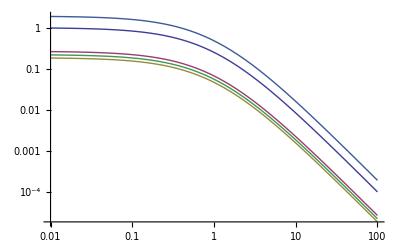

{{α→0},{α→0},{α→0},{α→2}}

```mathematica
p2[l_,η_]:=(1+η)/α Exp[-l (1+η)/α]
v2=Assuming[α≥1,var[p2,eabsA,η]]
FullSimplify[%/.α->1]
Needs["PlotLegends`"]
LogLogPlot[{
v2/.α->1,
v2/.α->1.5,
v2/.α->2,
v2/.α->2.5,
v2/.α->10
},{η,0.01,100},PlotLegend->{1,1.5,2,2.5,10},LegendPosition->{0,-1.5}]
Solve[D[(2α^4)/(-1+2 α)^3,α]==0,α]
```

#### 3 - Biased on scattering opacity

It turns out, this isn’t a good thing to do. Total opacity biasing is always superior.

-1/(1+η)^2+(2 α^4 (1+η)^2)/(η (-η+2 α (1+η))^3)

(2+η^3 (2+η))/(η (1+η)^2 (2+η)^3)

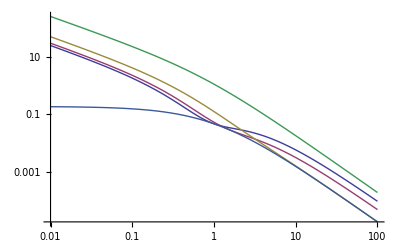

```mathematica
p3[l_,η_]:=η/α Exp[-l η/α]
v3=Assuming[α≥1,var[p3,eabsA,η]]
FullSimplify[%/.α->1]
Needs["PlotLegends`"]
LogLogPlot[{
v3/.α->1,
v3/.α->1.2,
v3/.α->2,
v3/.α->10,
v2/.α->2
},{η,0.01,100},PlotLegend->{1,1.2,2,10,"Total Opacity Biasing"},LegendPosition->{0,-1.5}]
```

#### 4 - Biased on absorption opacity

It turns out, this is also a bad thing to do. Biasing on total opacity is always superior.

-1/(1+η)^2+(2 α^4 (1+η)^2)/(-1+2 α (1+η))^3

(1+2 (η+η^4))/((1+η)^2 (1+2 η)^3)

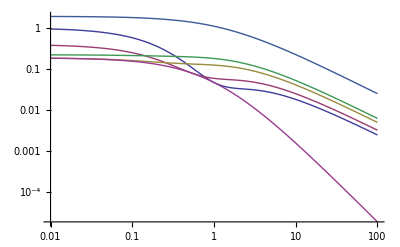

```mathematica
p4[l_,η_]:=1/α Exp[-l/α]
v4=Assuming[α≥1,var[p4,eabsA,η]]
FullSimplify[%/.α->1]
Needs["PlotLegends`"]
LogLogPlot[{
v4/.α->1,
v4/.α->1.3,
v4/.α->2,
v4/.α->2.5,
v4/.α->10,
v2/.α->2
},{η,0.01,100},PlotLegend->{1,1.3,2,2.5,10,"Total Opacity Biasing"},LegendPosition->{0,-1.5}]
```

#### 1 - Explicit Case

Move packet a distance according to the scattering opacity and reduce packet energy exponentially.
It turns out calculating everything explicitly is far more accurate than the standard technique, especially when absorption dominated. However, biasing the total opacity with α=2 wins when η>5/11.

(α^2 η)/((α+η)^2 (2 α+η))

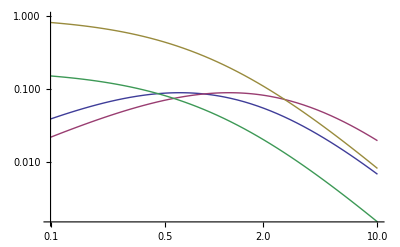

{{η→5/11}}

```mathematica
(*p1[l_,η_]:=η/α Exp[-η l/α]*)
v1=Assuming[{α≥1,η>0},var[p3,eabsB,η]]
Needs["PlotLegends`"]
LogLogPlot[{
v1/.α->1,
v1/.α->2,
v2/.α->1,
v2/.α->2
},{η,0.1,10},PlotLegend->{"1","2","Total Opacity Biasing alpha=1","Total Opacity Biasing alpha=2"},LegendPosition->{0,-1.5}]
Solve[(v2/.α->2)==(v1/.α->1),η]
```

```mathematica
Simplify[e[p1,l,η]]
Simplify[e[p3,l,η]/.α->1]
```

(ⅇ^-l (1+η))/η

(ⅇ^-l (1+η))/η